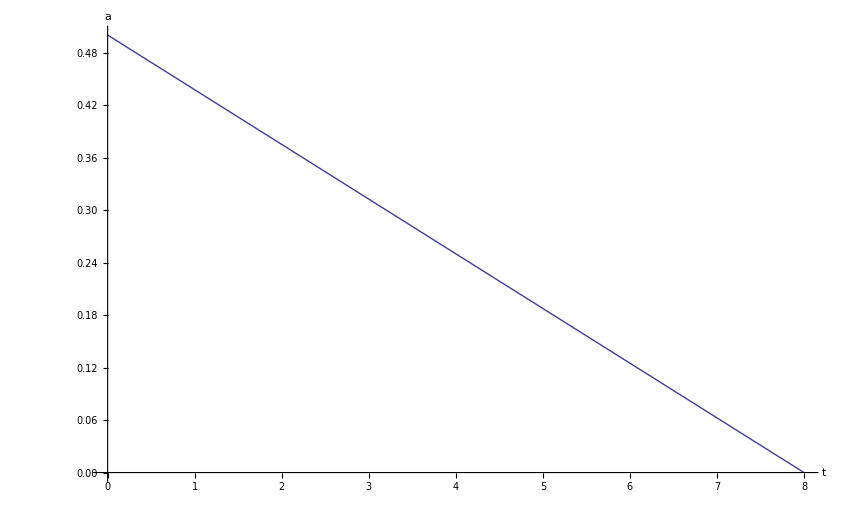

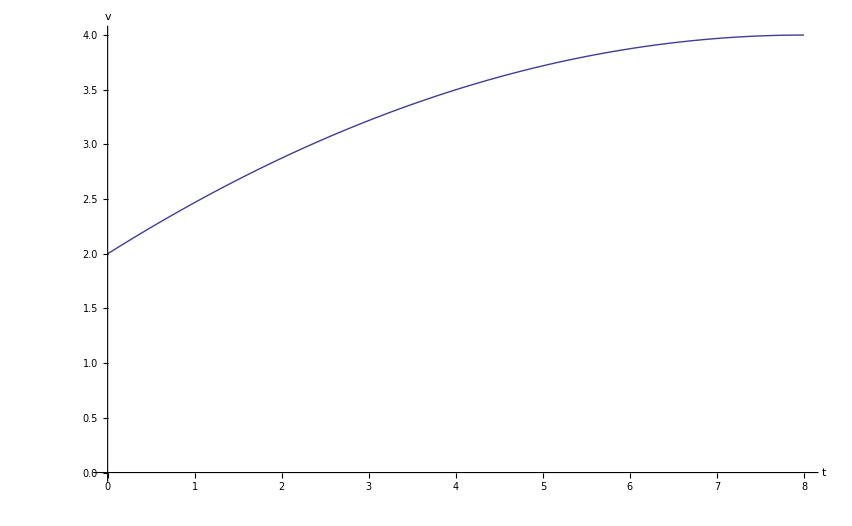

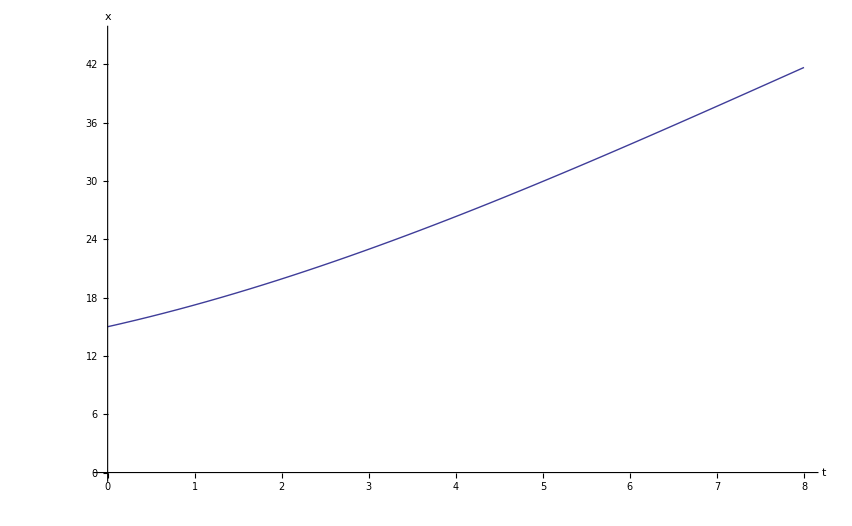

```mathematica
a0=0.5;
T=8;
vi=2;
xi=15;
Plot[a0(1-t/T),{t,0,T},AxesLabel->{t,a},AxesStyle->Large,PlotStyle->Thick]
Plot[vi+a0(t-t^2/(2T)),{t,0,T},AxesLabel->{t,v},AxesStyle->Large,PlotStyle->Thick,PlotRange->{0,4}]
Plot[xi+vi t+a0(t^2/2-t^3/(6T)),{t,0,T},AxesLabel->{t,x},AxesStyle->Large,PlotStyle->Thick,PlotRange->{0,45}]
```